{{x→-1.09303},{x→-0.803086},{x→1.00976}}

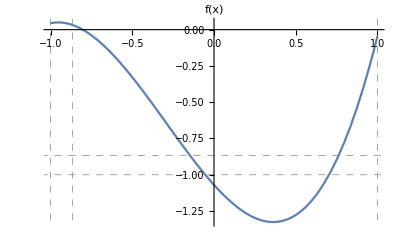

{-0.00984848,0.139197}

-Graphics-

```mathematica
nd = 10;
L= nd*(nd-1)/2;
tospin[x_]:=2*x-1
toedge[x_]:=(1+x)/2


(***** Matching Random Graphs *****)
μ=1/L//N;
ρ = 5*10^3;
φ = ρ * μ//N;
EE= 3//N;
d0=1.0;

f[x_]=-2*μ*x-φ /L^2*(1-x^2)((L-1)/2.*x+L/2.-EE);
Solve[f[x]==0,x]
(* Plots f(x) *)
Plot[{-2*μ*x-ρ /L^3*(1-x^2)((L-1)/2.*x+L/2.-EE)},{x,-1,1},AxesLabel->{None,"f(x)"},GridLines->{{-1,tospin[EE/L],1}},GridLinesStyle->Directive[Gray, Dashed]]
Manipulate[Plot[{-2*μ*x-ρ /L^3*(1-x^2)((L-1)/2.*x+L/2.-EE)},{x,-1,1},AxesLabel->{None,"f(x)"},GridLines->{{-1,tospin[EE/L],1}},GridLinesStyle->Directive[Gray, Dashed]],{μ,0.001,0.01,Appearance->"Labeled"},{ρ,1,100,Appearance->"Labeled"}];

asymMRG[μ0_,φ0_]:=
Module[{a=μ0,b=φ0 },
f0[x_]=-2*a*x-b/L^2*(1-x^2)((L-1)/2.*x+L/2.-EE);
asymvalue=x/.Solve[f0[x]==0,x][[2]];
asymvalue
]

μ0=2/L-Range[0.2/L,2/L,0.2/L];
φ0=Range[1000,10000,2000]/L //N;
spindensity = Table[asymMRG[μ0[[i]],φ0[[j]]],{i,1,Length[μ0]},{j,1,Length[φ0]}];

{xticks,yticks}=MapIndexed[{#2[[1]],#}&,#]&/@{μ0,φ0};

minmax = MinMax[toedge[spindensity]-EE/L]
p3= MatrixPlot[toedge[spindensity]-EE/L,ColorFunction->ColorData[{"TemperatureMap",minmax}],ColorFunctionScaling->False,PlotLabel->Style["Asymptotic Graph Density",12] ,PlotLegends->Automatic,FrameTicks->{MapAt[ScientificForm@#&,yticks,{All,2}],MapAt[Rotate[ScientificForm@#,45 Degree]&,yticks,{All,2}]},FrameLabel->{"μ","φ"}]
Export["./Downloads/mrg-1.pdf",p3];
```

100

-1.06996-1.25158 x+1.06996 x^2+1.20713 x^3

{{x→InterpolatingFunction[…]}}

{0.0984572}

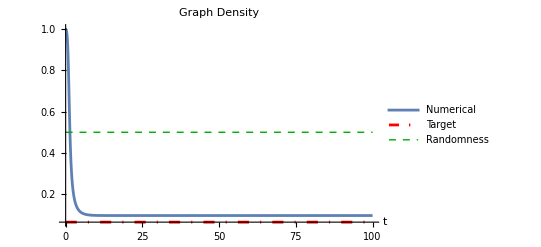

./Downloads/mrg-2.pdf

```mathematica
T = 100
fs[x]=f[x]//Simplify
s=NDSolve[{x'[t]==fs[x[t]],x[0]==tospin[d0]},x,{t,0,T}]
toedge[x[T]/.s]
p4= Plot[{Evaluate[toedge[x[t]/.s]], EE/L,toedge[0]},{t,0,T},
PlotStyle->{Directive[AbsoluteThickness[2],Opacity[1],Violet],Directive[AbsoluteThickness[2],Dashing[{.02,.02,.002, .02}], Red],Directive[AbsoluteThickness[1],Dashed, Darker@Green]},
PlotLegends->Placed[{Numerical , Target ,Randomness},Below],PlotLabel->Style["Graph Density",12],AxesLabel->{t,None},PlotRange->All]
Export["./Downloads/mrg-2.pdf",p4]
```

```mathematica
100
```

100